# ToneAr/RocketChat

A Wolfram Language service connection to Rocket.Chat REST API

## Paclet Manifest

"Documentation"

"English"

"Guides"

"ReferencePages"

"Services"

"Rocket.Chat.nb"DocumentationEnglishReferencePagesServicesRocket.Chat.nb

"Symbols"

"t.nb"DocumentationEnglishReferencePagesSymbolst.nb

"Tutorials"

"Kernel"

"Private.wl"KernelPrivate.wl

"RocketChat.wl"KernelRocketChat.wl

"Source"

"Globals.wl"KernelSourceGlobals.wl

"RawRequests"

"ABAC.wl"KernelSourceRawRequestsABAC.wl

"Apps.wl"KernelSourceRawRequestsApps.wl

"Assets.wl"KernelSourceRawRequestsAssets.wl

"Authentication.wl"KernelSourceRawRequestsAuthentication.wl

"AutoTranslate.wl"KernelSourceRawRequestsAutoTranslate.wl

"Banners.wl"KernelSourceRawRequestsBanners.wl

"CalendarEvents.wl"KernelSourceRawRequestsCalendarEvents.wl

"Channels.wl"KernelSourceRawRequestsChannels.wl

"Chat.wl"KernelSourceRawRequestsChat.wl

"Cloud.wl"KernelSourceRawRequestsCloud.wl

"CustomSounds.wl"KernelSourceRawRequestsCustomSounds.wl

"CustomStatus.wl"KernelSourceRawRequestsCustomStatus.wl

"Directory.wl"KernelSourceRawRequestsDirectory.wl

"DM.wl"KernelSourceRawRequestsDM.wl

"DNS.wl"KernelSourceRawRequestsDNS.wl

"E2E.wl"KernelSourceRawRequestsE2E.wl

"EmailInbox.wl"KernelSourceRawRequestsEmailInbox.wl

"Emoji.wl"KernelSourceRawRequestsEmoji.wl

"EngagementDashboard.wl"KernelSourceRawRequestsEngagementDashboard.wl

"Federation.wl"KernelSourceRawRequestsFederation.wl

"Groups.wl"KernelSourceRawRequestsGroups.wl

"Import.wl"KernelSourceRawRequestsImport.wl

"Instances.wl"KernelSourceRawRequestsInstances.wl

"Integrations.wl"KernelSourceRawRequestsIntegrations.wl

"Invites.wl"KernelSourceRawRequestsInvites.wl

"LDAP.wl"KernelSourceRawRequestsLDAP.wl

"Licenses.wl"KernelSourceRawRequestsLicenses.wl

"Livechat.wl"KernelSourceRawRequestsLivechat.wl

"Mailer.wl"KernelSourceRawRequestsMailer.wl

"Misc.wl"KernelSourceRawRequestsMisc.wl

"Moderation.wl"KernelSourceRawRequestsModeration.wl

"OAuthApps.wl"KernelSourceRawRequestsOAuthApps.wl

"Permissions.wl"KernelSourceRawRequestsPermissions.wl

"Push.wl"KernelSourceRawRequestsPush.wl

"Roles.wl"KernelSourceRawRequestsRoles.wl

"Rooms.wl"KernelSourceRawRequestsRooms.wl

"Sessions.wl"KernelSourceRawRequestsSessions.wl

"Settings.wl"KernelSourceRawRequestsSettings.wl

"SlashCommands.wl"KernelSourceRawRequestsSlashCommands.wl

"Statistics.wl"KernelSourceRawRequestsStatistics.wl

"Subscriptions.wl"KernelSourceRawRequestsSubscriptions.wl

"Teams.wl"KernelSourceRawRequestsTeams.wl

"Users.wl"KernelSourceRawRequestsUsers.wl

"VideoConference.wl"KernelSourceRawRequestsVideoConference.wl

"WebDAV.wl"KernelSourceRawRequestsWebDAV.wl

"Requests.wl"KernelSourceRequests.wl

"Utilities.wl"KernelSourceUtilities.wl

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinitions.nb"ResourceDefinitions.nb

"Resources"

"icon.svg"Resourcesicon.svg

"RocketChat.dev.nb"RocketChat.dev.nb

"testing.vsnb"testing.vsnb

"Tests"

"docker-compose.yml"Testsdocker-compose.yml

"RocketChatTests.wlt"TestsRocketChatTests.wlt

"RunTests.wls"TestsRunTests.wls

"setup.sh"Testssetup.sh

"teardown.sh"Teststeardown.sh

"TestHelpers.wl"TestsTestHelpers.wl

## Web Content

### Headline Image

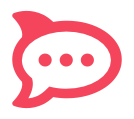

### Basic Description

Service connection to Rocket.Chat REST API.

### Details

Exclusively exposed through the ServiceFramework with no public symbols.

Supports interactive and programmatic authentication.

### Primary Context

ToneAr`RocketChat`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
Quit
```

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
Get["ToneAr`RocketChat`"];
```

### Basic Examples

Create a service connection to RocketChat:

```mathematica
con = ServiceConnect["Rocket.Chat"]
```

ServiceObject[…]

Send a direct message to a room:

```mathematica
ServiceExecute[con,
 	"SendMessage", {
  		"Message" -> <|
    			"msg" -> "Hello from the Wolfram Language",
    			"rid" -> "M8QWvkEPnaSmT6mAY"
    		|>
  	}
 ]
```

Success[…]

The full response object is available inside the Success object:

```mathematica
Keys[%[[2]]]
```

{message,success,MessageTemplate,MessageParameters}

Dispose the service connection:

```mathematica
ServiceDisconnect[con]
```

## Source & Additional Information

### Creator

Antonis Aristeidou

### Source Control Repository

https://github.com/ToneAr/RocketChatLink

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

Rocket

Chat

Instant

Messaging

Service

Connect

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

### Original Source References and Attributions

### Links

https://developer.rocket.chat/apidocs

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

### 1.0.0 | 2026-05-13